```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 263 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[rm]
rm = { x[t] , y[t] }
```

{x[t],y[t]}

```mathematica
D[rm, t]
```

{x'[t],y'[t]}

```mathematica
D[rm, t] . D[rm, t]
```

x'[t]^2+y'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[rm, t] . D[rm, t]  )
```

1/2 m (x'[t]^2+y'[t]^2)

```mathematica
Clear[r1]
r1 = { -1 , 1 } 
Clear[r2]
r2 = { 1 , 1 } 
Clear[r3]
r3 = { -1 , -1 } 
Clear[l0]
l0 = √2
```

{-1,1}

{1,1}

{-1,-1}

√2

```mathematica
Clear[r]
r = { r1 , r2 , r3 }
```

{{-1,1},{1,1},{-1,-1}}

```mathematica
r1
r1[[1]]
r1[[2]]
```

{-1,1}

-1

1

```mathematica
( √(( x[t] - r1[[1]] )^2+ ( y[t]-r1[[2]] )^2)  - l0  )^2
```

(-√2+√((1+x[t])^2+(-1+y[t])^2))^2

```mathematica
Table[( √(( x[t] - r[[i,1]] )^2+ ( y[t]-r[[i,2]] )^2)  - l0  )^2 , { i , 1 , 3 } ]  //  TableForm
```

(-√2+√((1+x[t])^2+(-1+y[t])^2))^2
(-√2+√((-1+x[t])^2+(-1+y[t])^2))^2
(-√2+√((1+x[t])^2+(1+y[t])^2))^2

```mathematica
Sum[ ( √(( x[t] - r[[i,1]] )^2+ ( y[t]-r[[i,2]] )^2)  - l0  )^2 , { i , 1 , 3 } ]
```

(-√2+√((-1+x[t])^2+(-1+y[t])^2))^2+(-√2+√((1+x[t])^2+(-1+y[t])^2))^2+(-√2+√((1+x[t])^2+(1+y[t])^2))^2

```mathematica
Clear[V]
V = 
1/2 K Sum[ ( √(( x[t] - r[[i,1]] )^2+ ( y[t]-r[[i,2]] )^2)  - l0  )^2 , { i , 1 , 3 } ] ;
V // TraditionalForm
```

1/2 K ((√((x(t)-1)^2+(y(t)-1)^2)-√2)^2+(√((x(t)+1)^2+(y(t)-1)^2)-√2)^2+(√((x(t)+1)^2+(y(t)+1)^2)-√2)^2)

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

1/2 m (((∂x(t))/(∂t))^2+((∂y(t))/(∂t))^2)-1/2 K ((√((x(t)-1)^2+(y(t)-1)^2)-√2)^2+(√((x(t)+1)^2+(y(t)-1)^2)-√2)^2+(√((x(t)+1)^2+(y(t)+1)^2)-√2)^2)

```mathematica
Clear[q]
q = { x[t] , y[t] }
```

{x[t],y[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ]  
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ]
```

1/2 K ((2 (-1+x[t]) (-√2+√((-1+x[t])^2+(-1+y[t])^2)))/(√((-1+x[t])^2+(-1+y[t])^2))+(2 (1+x[t]) (-√2+√((1+x[t])^2+(-1+y[t])^2)))/(√((1+x[t])^2+(-1+y[t])^2))+(2 (1+x[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2)))+m x''[t]

1/2 K ((2 (-√2+√((-1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((-1+x[t])^2+(-1+y[t])^2))+(2 (-√2+√((1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((1+x[t])^2+(-1+y[t])^2))+(2 (1+y[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2)))+m y''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ]  == 0 , 
{ i, 1, 2 } ] // TableForm
```

1/2 K ((2 (-1+x[t]) (-√2+√((-1+x[t])^2+(-1+y[t])^2)))/(√((-1+x[t])^2+(-1+y[t])^2))+(2 (1+x[t]) (-√2+√((1+x[t])^2+(-1+y[t])^2)))/(√((1+x[t])^2+(-1+y[t])^2))+(2 (1+x[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2)))+m x''[t]==0
1/2 K ((2 (-√2+√((-1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((-1+x[t])^2+(-1+y[t])^2))+(2 (-√2+√((1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((1+x[t])^2+(-1+y[t])^2))+(2 (1+y[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2)))+m y''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-(K (-1+x[t]) (-√2+√((-1+x[t])^2+(-1+y[t])^2)))/(√((-1+x[t])^2+(-1+y[t])^2))-(K (1+x[t]) (-√2+√((1+x[t])^2+(-1+y[t])^2)))/(√((1+x[t])^2+(-1+y[t])^2))-(K (1+x[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2))-m x''[t]==0
-(K (-√2+√((-1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((-1+x[t])^2+(-1+y[t])^2))-(K (-√2+√((1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((1+x[t])^2+(-1+y[t])^2))-(K (1+y[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2))-m y''[t]==0

```mathematica
Clear[parameters]
parameters = { 
K-> 200 , 
m-> 5 
} ;
parameters // TableForm
```

K→200
m→5

```mathematica
eqs /. parameters  // TableForm
```

-(200 (-1+x[t]) (-√2+√((-1+x[t])^2+(-1+y[t])^2)))/(√((-1+x[t])^2+(-1+y[t])^2))-(200 (1+x[t]) (-√2+√((1+x[t])^2+(-1+y[t])^2)))/(√((1+x[t])^2+(-1+y[t])^2))-(200 (1+x[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2))-5 x''[t]==0
-(200 (-√2+√((-1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((-1+x[t])^2+(-1+y[t])^2))-(200 (-√2+√((1+x[t])^2+(-1+y[t])^2)) (-1+y[t]))/(√((1+x[t])^2+(-1+y[t])^2))-(200 (1+y[t]) (-√2+√((1+x[t])^2+(1+y[t])^2)))/(√((1+x[t])^2+(1+y[t])^2))-5 y''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0.2 , 
x'[0] == 0 , 
y[0] == - 0.1 , 
y'[0] == 0 } ;
ics // TableForm
```

x[0]==0.2
x'[0]==0
y[0]==-0.1
y'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters, ics ] , q, { t, 0, 300 } ]   ]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q/. solution[t] ]  , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

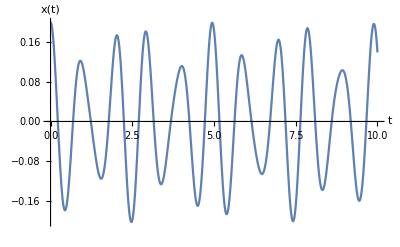

```mathematica
Plot[ q[[1]]/. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,300 , 0.5  } ]
```

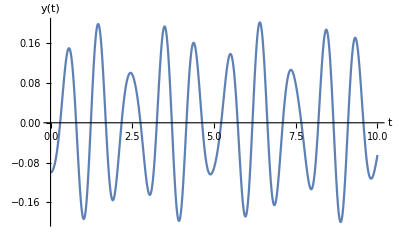

```mathematica
Plot[ q[[2]]/. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```